```mathematica
Clear["Global`*"];
```

## All double pass

### MOT

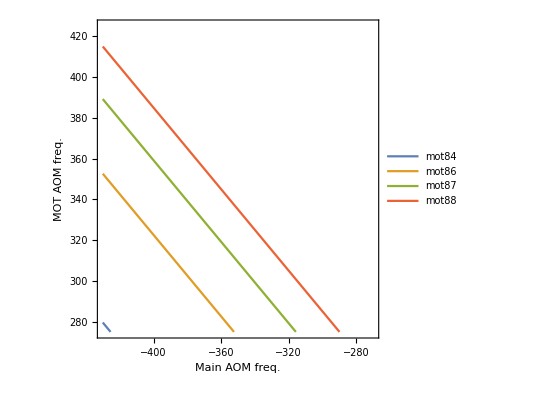

```mathematica
ContourPlot[{2*(omegamain+omegamot)==-300.8,2*(omegamain+omegamot)==-154.8,2*(omegamain+omegamot)==-81.6,2*(omegamain+omegamot)==-30.0},{omegamain,-430,-270},{omegamot,275,425},Axes->True,FrameLabel->{"Main AOM freq.","MOT AOM freq."},PlotLegends->{"mot84","mot86","mot87","mot88"}]
```

### TC

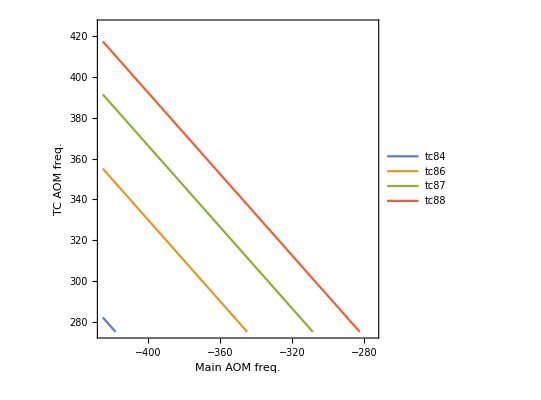

```mathematica
ContourPlot[{2*(omegamain+omegatc)==-285.8,2*(omegamain+omegatc)==-139.8,2*(omegamain+omegatc)==-67,2*(omegamain+omegatc)==-15.0},{omegamain,-425,-275},{omegatc,275,425},Axes->True,FrameLabel->{"Main AOM freq.","TC AOM freq."},PlotLegends->{"tc84","tc86","tc87","tc88"}]
```

### ZS

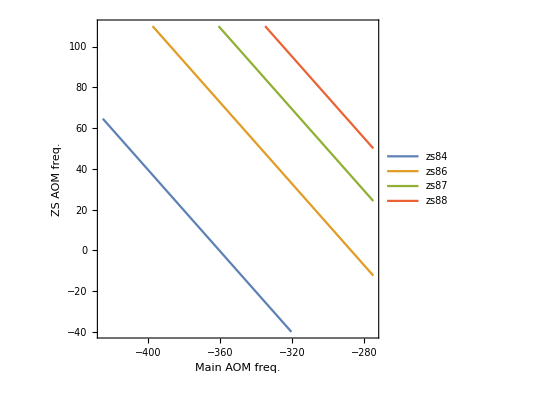

```mathematica
ContourPlot[{2*(omegamain+omegazs)==-720.8,2*(omegamain+omegazs)==-574.8,2*(omegamain+omegazs)==-501.6,2*(omegamain+omegazs)==-450},{omegamain,-425,-275},{omegazs,-40,110},Axes->True,FrameLabel->{"Main AOM freq.","ZS AOM freq."},PlotLegends->{"zs84","zs86","zs87","zs88"}]
```

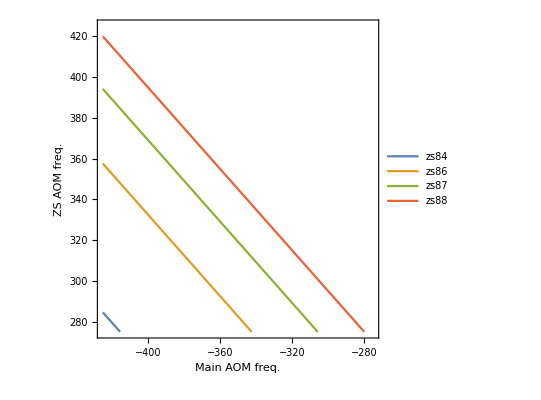

```mathematica
ContourPlot[{2*(omegamain-220+omegazs)==-720.8,2*(omegamain-220+omegazs)==-574.8,2*(omegamain-220+omegazs)==-501.6,2*(omegamain-220+omegazs)==-450},{omegamain,-425,-275},{omegazs,275,425},Axes->True,FrameLabel->{"Main AOM freq.","ZS AOM freq."},PlotLegends->{"zs84","zs86","zs87","zs88"}]
```

```mathematica
Manipulate[ContourPlot[{2*(omegamain+additional+omegazs)==-720.8,2*(omegamain+additional+omegazs)==-574.8,2*(omegamain+additional+omegazs)==-501.6,2*(omegamain+additional+omegazs)==-450},{omegamain,-425,-275},{omegazs,-425,425},Axes->True,FrameLabel->{"Main AOM freq.","ZS AOM freq."},PlotLegends->{"zs84","zs86","zs87","zs88"}],{additional,-425,425}]
```

### Imaging

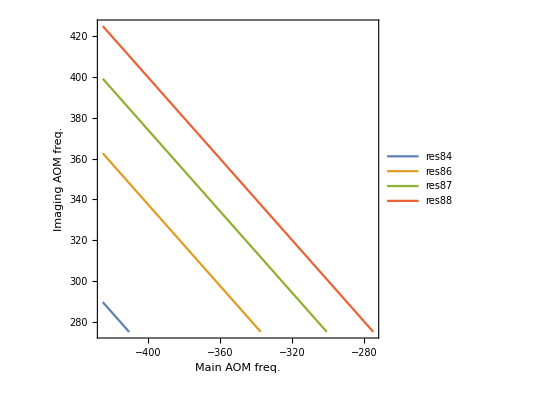

```mathematica
ContourPlot[{2*(omegamain+omegares)==-270.8,2*(omegamain+omegares)==-124.8,2*(omegamain+omegares)==-51.6,2*(omegamain+omegares)==0},{omegamain,-425,-275},{omegares,275,425},Axes->True,FrameLabel->{"Main AOM freq.","Imaging AOM freq."},PlotLegends->{"res84","res86","res87","res88"}]
```

## Single pass on the second one

### ZS

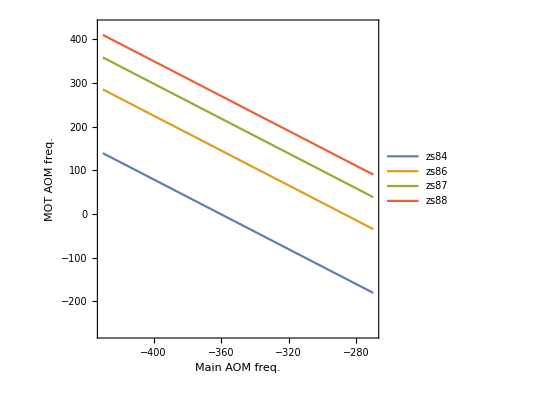

```mathematica
ContourPlot[{2*omegamain+omegazs==-720.8,2*omegamain+omegazs==-574.8,2*omegamain+omegazs==-501.6,2*omegamain+omegazs==-450},{omegamain,-430,-270},{omegazs,-270,430},Axes->True,FrameLabel->{"Main AOM freq.","MOT AOM freq."},PlotLegends->{"zs84","zs86","zs87","zs88"}]
```